# BPMF Mick Ramsey

## Initial Condition/Import Data

```mathematica
Clear["Global`*"]
Needs["MultivariateStatistics`"]
```

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
dim=10; (*Dimension of Latenet Features*)
β0=2.;
W0=N[IdentityMatrix[dim]]; (*Hyperparameter*)
μ0=N[Transpose[{ConstantArray[0,dim]}]];(*Hyperparameter*)
ν0=10. (*Hyperparameter*)
```

```mathematica
Vj=Import["/Users/mick/Desktop/PROJECT/ImportData/movie.csv"];
Ui=Import["/Users/mick/Desktop/PROJECT/ImportData/user.csv"];
matrixdata=Import["/Users/mick/Desktop/PROJECT/ImportData/netflixdata.csv"];
probedata=Import["/Users/mick/Desktop/PROJECT/ImportData/probedata.csv"];
traindata=Import["/Users/mick/Desktop/PROJECT/ImportData/traindata.csv"];
```

```mathematica
spMD=SparseArray[matrixdata];
```

## Equations

```mathematica
uu=probedata[[All,1]]; (*list users in probe data set*)
vv=probedata[[All,2]];(*list of rated movies in probe data set*)
ratings=N[probedata[[All,3]]]; (*Rating cooresponding to user movie combition*)
meanrating=N[Mean[traindata[[All,3]]]];
d=Transpose[spMD]["AdjacencyLists"];
c=spMD["AdjacencyLists"];
rij=ReplaceAll[DeleteCases[0]/@Transpose[matrixdata],{}->ConstantArray[0,1]];
rij2=Select[DeleteCases[0]/@matrixdata,UnsameQ[#,{}]&];
AB=ReplaceAll[Map[(Ui[[#,All]])&,d],{}->ConstantArray[0,{1,dim}]];
BA=Map[(Vj[[#,All]])&,c];
```

```mathematica
iW[iAB_]:=With[{Nuv=N[Length[iAB]],Suv=N[Covariance[iAB]],Xuv=N[Transpose[{Mean[iAB]}]]},(Inverse[Inverse[W0]+Nuv Suv+(β0 Nuv)/(β0+Nuv)*(μ0-Xuv).Transpose[μ0-Xuv]]+Transpose[Inverse[Inverse[W0]+Nuv Suv+(β0 Nuv)/(β0+Nuv)*(μ0-Xuv).Transpose[μ0-Xuv]]])/2];
iL[iAB_,Λ_]:=Transpose[CholeskyDecomposition[(Inverse[(β0+N[Length[iAB]])*Λ]+Transpose[Inverse[(β0+N[Length[iAB]])*Λ]])/2]]
iΛuv[iAB_]:=With[{W=iW[iAB],ν=ν0+N[Length[iAB]]},RandomVariate[WishartDistribution[W,ν]]]
iμuv[iAB_,Λ_]:=With[{L=iL[iAB,Λ],μ=(β0 μ0+N[Length[iAB]] N[Transpose[{Mean[iAB]}]])/(β0+N[Length[iAB]])},μ+L.RandomVariate[NormalDistribution[0,1],dim]]
```

```mathematica
μmean[Λ_,uv_,r_,ΛC_,μC_]:=Λ.(β0*Transpose[uv].(r-meanrating)+ΛC.μC)
Λcovar[uv_,ΛC_]:=(Inverse[ΛC+β0*Transpose[uv].uv]+Transpose[Inverse[ΛC+β0*Transpose[uv].uv]])/2
UVlat[λ_,μm_]:=Flatten[λ.RandomVariate[NormalDistribution[0,1],dim]+μm]
```

## Module

```mathematica
bArray={};
aArray={};
eArray={};
```

```mathematica
proball=Total[Vj[[aam]]*Ui[[aap]],{2}]+meanrating ;
counterprobe=1;
```

```mathematica
Monitor[Do[
iΛv=iΛuv[Vj];
iμv=iμuv[Vj,iΛv];

iΛu=iΛuv[Ui];
iμu=iμuv[Ui,iΛu];


Monitor[Do[
iΛ=MapThread[Λcovar,{AB,ConstantArray[iΛv,Dimensions[AB]]}];
iλ=MapThread[CholeskyDecomposition,{iΛ}];
iα=MapThread[μmean,{iΛ,AB,rij,ConstantArray[iΛv,Dimensions[AB]],ConstantArray[iμv,Dimensions[AB]]}];
Vj=MapThread[UVlat,{iλ,iα}];


iΛ=MapThread[Λcovar,{BA,ConstantArray[iΛu,Dimensions[BA]]}];
iλ=MapThread[CholeskyDecomposition,{iΛ}];
iα=MapThread[μmean,{iΛ,BA,rij2,ConstantArray[iΛu,Dimensions[BA]],ConstantArray[iμu,Dimensions[BA]]}];
Ui=MapThread[UVlat,{iλ,iα}];

,{tt,1,2}(*Thining of 50%*)

],{tt,ProgressIndicator[tt,{1,2}]}];

AppendTo[bArray,Vj];
AppendTo[aArray,Ui];


prediction=Total[Vj[[vv]]*Ui[[uu]],{2}]+meanrating;
proball=(counterprobe*proball+prediction)/(counterprobe+1);
counterprobe=counterprobe+1;
rms=(ratings-proball)^2;
err=(Total[rms]/N[Length[probedata]])^(1/2);
AppendTo[eArray,err];

,
{t,1,5000}

],{t,ProgressIndicator[t,{1,5000}]}];//AbsoluteTiming
```

{16781.06003,Null}

## Results and Graphs

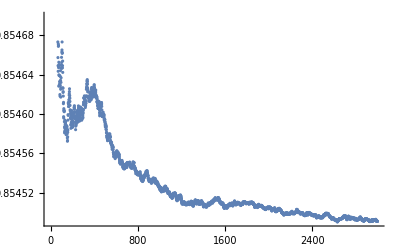

```mathematica
ListPlot[eArray]
```

```mathematica
fu[x_,y_]:={aArray[[x]][[y]]}.Transpose[{aArray[[x]][[y]]}]
fv[x_,y_]:={bArray[[x]][[y]]}.Transpose[{bArray[[x]][[y]]}]
```

```mathematica
udata=Flatten[Table[fu[x,1],{x,1,300}]];
ListLinePlot[udata]
```

Part::partd: Part specification iUArray ⟦ 1 ⟧ is longer than depth of object.

Transpose::nmtx: The first two levels of {iUArray} cannot be transposed.

Part::partd: Part specification iUArray ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {iUArray} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

-Graphics-

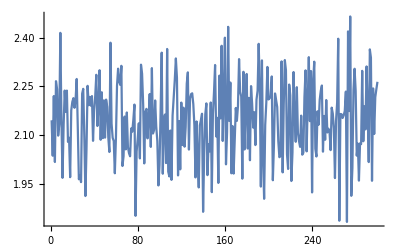

```mathematica
vdata=Flatten[Table[fv[x,1],{x,1,300}]];
ListLinePlot[vdata]
```

```mathematica
ui[x_,y_,z_]:=aArray[[x]][[y]][[z]]
vi[x_,y_,z_]:=bArray[[x]][[y]][[z]]
```

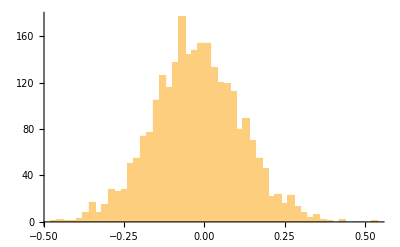

```mathematica
Histogram[Table[vi[x,2567,1],{x,400,3000}],40]
```

```mathematica
Histogram3D[Table[vi[x,323,{3,4}],{x,800,1800}],60]
```

-Graphics3D-

```mathematica
cosine[x1_,x2_]:=({iVArray⟦1800⟧⟦x1⟧}.Transpose[{iVArray⟦1800⟧⟦x2⟧}])/(Norm[iVArray⟦1800⟧⟦x1⟧] Norm[iVArray⟦1800⟧⟦x2⟧])
```